# Correction Procedure via Reconstruction (CPR)

## CPR: Flux Reconstruction (FR) / Lifting Collocation Penalty (LCP)

## Coded by Manuel Diaz, NTU, 2013.08.20

Based on Ideas of jounal papers:

1. Z.J. Wang & Hai - Yang Gao, JCP 228 (2009) 8161-8186. -> (LCP)
2. H.T. Huynh, AIAA (2007) 4079.->  (FR)
3. Jie Du, Chi-Wang Shu, MengPing Zhang, Brown University (2013) 15.  -> (CPR)

Derivation of the Method in one-dimensional space.

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Initialize Symbols & Notation

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Change Notebook to it’s original colors

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Load Notation package and create symbols

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[u, j-1/2]^+];Symbolize[Subscript[u, j-1/2]^-];Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-];Symbolize[Subscript[u, j+1/2]^+];Symbolize[Subscript[f̂, j+1/2]];
```

## Review on Flux Reconstruction Method

### Building the Domain

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells/elements

```mathematica
a= 0; b = 1; n = 10; nodes = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define element sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define element centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Define Solution Points, ξ_k, inside the standar element:
We can use for example: four-Gauss Legendre Points,

```mathematica
(*abscissas = {-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}; *)
(* weights={1/36 (18-√30),1/36 (18+√30),1/36 (18+√30),1/36 (18-√30)}; *)
```

Or we can use also: four-Gauss-Lobatto Points,

```mathematica
abscissas = {-1,-1/(√5),1/(√5),1}; 
weights={1/6,5/6,5/6,1/6};
```

I, personally, prefer to call the abscissas ‘standar solution points’ or simply ‘solution points’. I will also  referer to all the points inside the domain as my ‘global nodes coordinates’.

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[w, 4]}=weights;
```

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (solution points here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ Subscript[h, j]/2 abscissas,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0. | 0.0276393 | 0.0723607 | 0.1
0.1 | 0.127639 | 0.172361 | 0.2
0.2 | 0.227639 | 0.272361 | 0.3
0.3 | 0.327639 | 0.372361 | 0.4
0.4 | 0.427639 | 0.472361 | 0.5
0.5 | 0.527639 | 0.572361 | 0.6
0.6 | 0.627639 | 0.672361 | 0.7
0.7 | 0.727639 | 0.772361 | 0.8
0.8 | 0.827639 | 0.872361 | 0.9
0.9 | 0.927639 | 0.972361 | 1.

Define ' u_(j,k)’ values for every node in our domain.
I will assume an IC as: u(x) = 0.5 +sin(2πx), therefore

```mathematica
Subscript[u, 𝒟]=0.5+Sin[2 π Subscript[x, 𝒟]];
Subscript[u, 𝒟]//TableForm
```

0.5 | 0.672791 | 0.939153 | 1.08779
1.08779 | 1.21874 | 1.38336 | 1.45106
1.45106 | 1.49015 | 1.49015 | 1.45106
1.45106 | 1.38336 | 1.21874 | 1.08779
1.08779 | 0.939153 | 0.672791 | 0.5
0.5 | 0.327209 | 0.0608471 | -0.0877853
-0.0877853 | -0.218735 | -0.383356 | -0.451057
-0.451057 | -0.490147 | -0.490147 | -0.451057
-0.451057 | -0.383356 | -0.218735 | -0.0877853
-0.0877853 | 0.0608471 | 0.327209 | 0.5

Load u_0 into our domain

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j=1 and k=2, we should get

```mathematica
Subscript[u, 1,2]
```

0.672791

```mathematica
(*Ok!*)
```

### Compute Fluxes in nodes

Let us compute the fluxes,' f_(j,k)’  at every node as well. 
Assume Burgers’ Flux: f(u) = u^2/2,

```mathematica
Subscript[f, 𝒟]= Subscript[u, 𝒟]^2/2;
```

```mathematica
Subscript[f, 𝒟] //TableForm
```

0.125 | 0.226324 | 0.441004 | 0.591638
0.591638 | 0.742658 | 0.956836 | 1.05278
1.05278 | 1.11027 | 1.11027 | 1.05278
1.05278 | 0.956836 | 0.742658 | 0.591638
0.591638 | 0.441004 | 0.226324 | 0.125
0.125 | 0.0535327 | 0.00185119 | 0.00385313
0.00385313 | 0.0239225 | 0.0734808 | 0.101726
0.101726 | 0.120122 | 0.120122 | 0.101726
0.101726 | 0.0734808 | 0.0239225 | 0.00385313
0.00385313 | 0.00185119 | 0.0535327 | 0.125

## Intermision I: Interpolation data

Define the k-lagrange polynomial for every value of u_(j,k) indise I_j:

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, j],Subscript[u, j]},{j,1,r}]
```

```mathematica
StencilPoints[4]
```

{{-1,u_1},{-1/(√5),u_2},{1/(√5),u_3},{1,u_4}}

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],u,Simplify]
```

```mathematica
Subscript[u, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
(* Testing *)
```

```mathematica
Subscript[u, j][-1]//N
```

u_1

```mathematica
Subscript[u, j][1]//N
```

u_4

```mathematica
(* Everything seems ok in this part *)
```

Similarly for the flux values f_j :

```mathematica
StencilPoints[r_] := Table[{Subscript[ξ, j],Subscript[f, j]},{j,1,r}]
```

```mathematica
StencilPoints[4]
```

{{-1,f_1},{-1/(√5),f_2},{1/(√5),f_3},{1,f_4}}

```mathematica
LagrangePolynomials[r_] := Collect[InterpolatingPolynomial[StencilPoints[r],ξ],f,Simplify]
```

```mathematica
Subscript[f, j][ξ_]:=Evaluate[LagrangePolynomials[4]]
```

```mathematica
(* Testing *)
Subscript[f, j][-1]//N
```

f_1

```mathematica
Subscript[f, j][1]//N
```

f_4

```mathematica
(* Good! *)
```

This result comes from interpolating ‘u’ values over the selected gauss Lobatto/ Solution points. ( equations 2.2 and 2.3 in [1], equations 6, 7 and 11 in [3] )

## Intermission II: Values at the faces of I_j

### Compute u values the faces

### Compute fluxes at the faces

```mathematica
Table[Subscript[f, j,k]= Subscript[f, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

At the boundary cells at ξ_1 and ξ_K (or ξ_4 for our example) immediatly we recognize them as (u_(j-1/2))^+= u_(j,1), and (u_(j+1/2))^-= u_(j,K)

To the right boundary of ‘ j+1/2’

```mathematica
SuperMinus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,4]];
SuperMinus[Subscript[u, j+1/2]] = Most[%];
SuperMinus[Subscript[u, j+1/2]] // TableForm
```

1.08779
1.45106
1.45106
1.08779
0.5
-0.0877853
-0.451057
-0.451057
-0.0877853

To the left boundary of ‘j+1/2’

```mathematica
SuperPlus[Subscript[u, j+1/2]] = Subscript[u, 𝒟][[All,1]];
SuperPlus[Subscript[u, j+1/2]] = Rest[SuperPlus[Subscript[u, j+1/2]]];
SuperPlus[Subscript[u, j+1/2]] // TableForm
```

1.08779
1.45106
1.45106
1.08779
0.5
-0.0877853
-0.451057
-0.451057
-0.0877853

### Numerical Flux

Compute Riemann Fluxes at the boundary points (using Lax-Friedrichs flux),

```mathematica
f[u_]:= u^2/2; df [u_]:=u;
```

```mathematica
α[a_,b_]:= Max[df[a],df[b]]
```

```mathematica
LF[a_,b_]:= 1/2(α[a,b](a-b)+(f[a]+f[b]))
```

```mathematica
Subscript[f̂, j+1/2]=LF[SuperMinus[Subscript[u, j+1/2]],SuperPlus[Subscript[u, j+1/2]]]; 
Subscript[f̂, j+1/2]//TableForm
```

0.591638
1.05278
1.05278
0.591638
0.125
0.00385313
0.101726
0.101726
0.00385313

## Intermision III: on the definion of correction function

Here, for the present example, we know that if we are using a reconstrunction using K=4 points, our u_(j,k) is degree k-1=3. Therefore we are interested in building a correction or order K , e.i. degree 4.
But how to do this?

In the literature we know that any correction function must fullfil the following requirements:
The function ℊ_LB(x) is the correction at the left boundary satisfying
	ℊ_LB(-1) = 1,	ℊ_LB(1) = 0;
The function ℊ_RB(x) is the correction at the right boundary satisfying
	ℊ_RB(-1) = 0,	ℊ_RB(1) = 1;

Now, Let me choose Radau Polynomials as the proposal of our correction functions:

### Build legendre Polynomials:

```mathematica
legendreP = Table[LegendreP[i,ξ],{i,0,5}];
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
```

### Radau Polynomials:

```mathematica
Subscript[Radau, left]= Table[1/2(Subscript[p, k]+Subscript[p, k-1]),{k,1,4}]//Expand//Simplify;
```

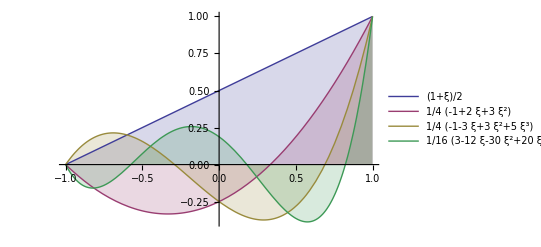

```mathematica
Plot[Evaluate[Subscript[Radau, left]],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Subscript[Radau, right]= Table[(-1)^k/2(Subscript[p, k]-Subscript[p, k-1]),{k,1,4}]//Simplify;
```

```mathematica
Table[Subscript[R, L,i]= Subscript[Radau, left][[i]],{i,1,4}];
```

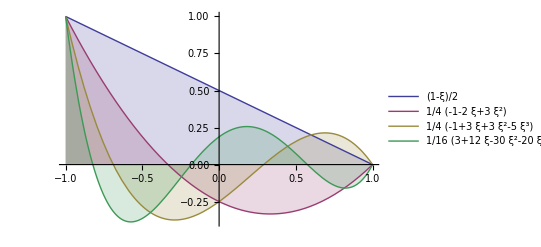

```mathematica
Plot[Evaluate[Subscript[Radau, right]],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[R, R,i]= Subscript[Radau, right][[i]],{i,1,4}];
```

Observe that Radau Polynomials full fill the above requirements very easily:

```mathematica
Subscript[R, R,4]/.ξ->-1
Subscript[R, R,4]/.ξ->1
```

1

0

```mathematica
Subscript[R, L,4]/.ξ->-1
Subscript[R, L,4]/.ξ->1
```

0

1

Therefore the Radau_right is a great candidate for g_LB.
and Radau_left is a great candidate for g_RB.

Evaluating the derivative of g_LB and g_RB in every solution points, we observe:

```mathematica
Subscript[dg, LB] = D[Subscript[R, R,4],ξ]/.ξ->abscissas//N;
Subscript[dg, RB] = D[Subscript[R, L,4],ξ]/.ξ->abscissas//N;
Subscript[dg, LB]//TableForm
Subscript[dg, RB] //TableForm
```

-8.
0.894427
-0.894427
2.

-2.
0.894427
-0.894427
8.

```mathematica
Subscript[dg, RB] == -Reverse[Subscript[dg, LB]]
```

True

Because of symmetry, we only need to consider ℊ_LB(x), or simply ℊ(x). It is more convenient to consider the correction function in the standar element g(ξ) on [-1,1]. It is claimed that using special Polynomials such as Radau and Legendre polynomials, the DG, SD (or SD/SV) methods can be succesfully recovered.

## Puting Everything Toguether

Based on Shu’s paper, the Continuous Flux Polynomial, F_j(ξ), must satisfy the following conditions:

1. The continuous Flux function F_j(ξ) should use the information of the flux at both side of every element  I_j face, namely
	F_j[-1] = (f̂)_(j-1/2)	and		F_j[1] =(f̂)_(j+1/2)

2. In each cell I_j, F_k(ξ) must be order K. i.e., one order higher than the solution polynomial u_j(ξ).

3. F_j(ξ) is required to approximate the discontinuous flux function f_j(ξ). 
 F_j(ξ) - f_j(ξ) a 0.

The continuous Flux Polynomial is then proposed to be

```mathematica
Subscript[F, j][ξ] = Subscript[f, j][ξ]+(Subscript[f̂, j-1/2]-Subscript[f, j][-1])Subscript[ℊ, LB][ξ]+(Subscript[f̂, j+1/2]-Subscript[f, j][1])Subscript[ℊ, RB][ξ] //N //TableForm
```

0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.591638-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(1.05278-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(1.05278-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.591638-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.125-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.00385313-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.101726-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.101726-1. f_4) ℊ_RB[ξ]
0.125 ((-1.+ξ+5. ξ^2-5. ξ^3) f_1+(1.+ξ) (5. (-1.+ξ) (-1.+2.23607 ξ) f_2-5. (-1.+ξ) (1.+2.23607 ξ) f_3+(-1.+5. ξ^2) f_4))+(-1. f_1+(f̂)_(-1/2+j)) ℊ_LB[ξ]+(0.00385313-1. f_4) ℊ_RB[ξ]